```mathematica
Exit[]
```

# Gamma qg

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
LaunchKernels[4];
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

#### Inputs

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
(* Singlet, large nf exact parts *)
Get[StringJoin[here, "singlet_nf3.m"]]
Get[StringJoin[here, "ns_nf3_nf2.m"]]
(* Singlet, asymptotic N-> Infinity, large nc limit *)
Get[StringJoin[here, "qcd_cusp.m"]]
(* Singlet, moments *)
Get[StringJoin[here, "gqq3nsp.m"]]
Get[StringJoin[here, "gqq3ps.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "ggg3.m"]]
```

```mathematica
Get[StringJoin[here, "fitting_utils.m"]]
Get[StringJoin[here, "plotting_utils.m"]]
Get[StringJoin[here, "saving_utils.m"]]
```

```mathematica
thrhigh = 10^-7;
thrlow = 10^-3;
gqgmoments = {gqg3N2,gqg3N4,gqg3N6,gqg3N8};

fsmallN = {1/(n-1)^2, 1/(n-1)^2, 1/(n-1)};
flargeN = {S13m1[n],S13m1[n],S13m1[n]};

fSubLeadingLargeN = {
	{1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm11[n],Lm11[n], Lm11[n]}, 
	{Lm12[n],Lm12[n], Lm12[n]}, 
	{Lm13[n],Lm13[n], Lm13[n]},
	{S12m1[n],S12m1[n],S12m1[n]},
	{S[1,n-2]/n,S[1,n-2]/n,S[1,n-2]/n} 
};
fSubLeadingSmallN = {
	{1/(n-1),1/(n-1),1/n},
	{1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n,1}
};
gqg3asy = MellinInverseSinglet[gqg3N0asy + gqg3N1asy + gqg3Ninf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
```

#### Cross candidates

Smooth candidates: 90 out of 91

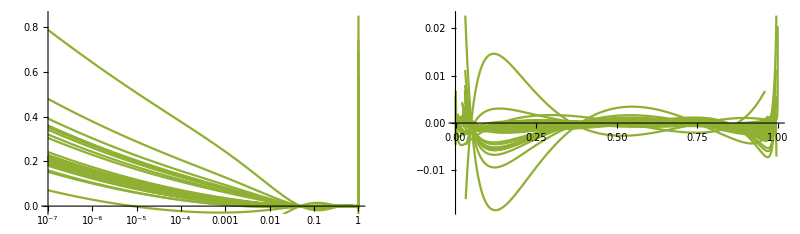

```mathematica
fSubLeadingtot = Join[fSubLeadingSmallN, fSubLeadingLargeN];
gqg3FittedCross = DoAllFits[fsmallN, flargeN, fSubLeadingtot, gqgmoments, gqg3N0asy, gqg3N1asy, gqg3Ninf];
gqg3invfull = ListMellinInverse[gqg3FittedCross];
gqg3inv = SelectSmoothCandidates[gqg3invfull, 4,thrlow,thrlow];
graphQGrep = PlotList[gqg3inv, gqg3asy, 4, 3] // Show;
graphQGlogrep = LogPlotList[gqg3inv, gqg3asy, 4, 3] // Show;
GraphicsRow[{graphQGlogrep,graphQGrep}]
```

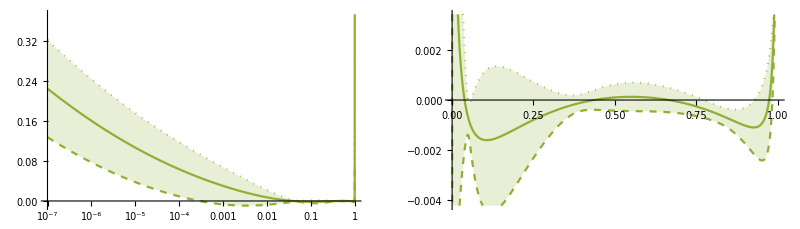

```mathematica
{graphQG,graphQGlog} =  PlotErrorBand[gqg3asy, gqg3inv, 4, 3];
GraphicsRow[{graphQGlog,graphQG}]
```

#### Cherry Picking

```mathematica
cherryfunctions = {1/n^4, Lm13[n]};
gqg3cherry = SelectCherriesSpecial[gqg3FittedCross, cherryfunctions];
gqg3cherry = SelectSmoothCandidates[gqg3cherry, 4, thrlow, thrhigh];
```

Selected cherries are: 25 out of 91

Smooth candidates: 22 out of 25

```mathematica
{graphQGcherry, graphQGcherrylog} = PlotErrorBand[gqg3asy, gqg3cherry, 4, 4]; 
legend = {"cross candidate", "cherries"}; 
GraphicsRow[{
    	ShowLegends[{graphQGlog, graphQGcherrylog}, LogLinearPlot, legend, {3, 4}], 
    	ShowLegends[{graphQG, graphQGcherry}, Plot, legend, {3, 4}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

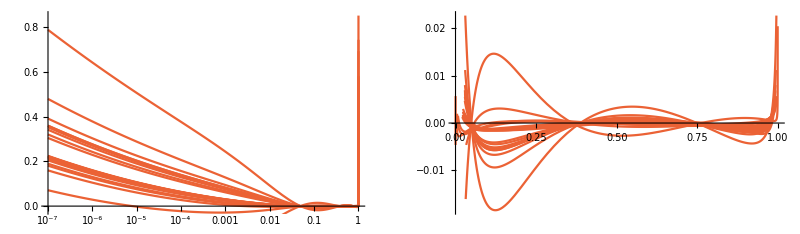

```mathematica
graphQGcherrylogrep = LogPlotList[gqg3cherry, gqg3asy, 4, 4];
graphQGcherryrep = PlotList[gqg3cherry, gqg3asy, 4, 4];
GraphicsRow[{Show[graphQGcherrylogrep], Show[graphQGcherryrep]}]
```

#### Plot nf^3

```mathematica
gqg3asy3 = Coefficient[gqg3asy, nf, 3];
gqg3inv3 =  SelectSmoothCandidates[Coefficient[gqg3inv, nf, 3], 4,thrlow,thrlow];
gqg3inv3cherries =  SelectSmoothCandidates[Coefficient[gqg3cherry, nf, 3], 4,thrlow,thrlow];
gqg3nf3x = gqg3nf3x /. QCDConstantsRules //N;
```

Smooth candidates: 89 out of 90

Smooth candidates: 31 out of 32

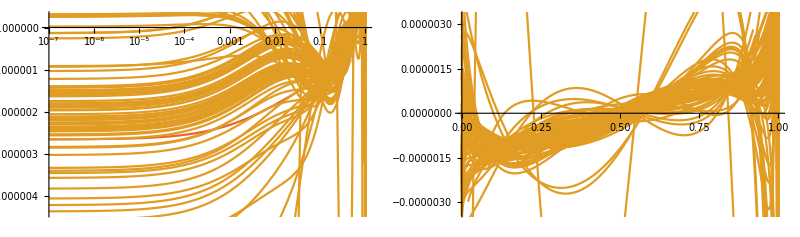

```mathematica
gtmp = PlotList[gqg3inv3, gqg3asy3, 4, 2];
gtmplog = LogPlotList[gqg3inv3, gqg3asy3, 4, 2];
graphQGExa3 = Plot[pifact gqg3nf3x, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphQGExa3log = LogLinearPlot[ pifact gqg3nf3x, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
GraphicsRow[{Show[{graphQGExa3log, gtmplog}], Show[{graphQGExa3, gtmp}]}, ImageSize->Full]
```

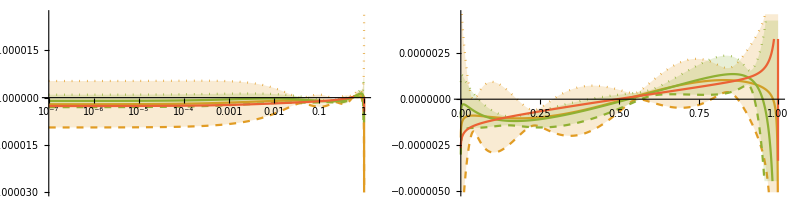

```mathematica
{graphQG3, graphQG3log} = PlotErrorBand[gqg3asy3, gqg3inv3, 4,2];
{graphQG3cherry, graphQG3cherrylog} = PlotErrorBand[gqg3asy3, gqg3inv3cherries, 4,3];
GraphicsRow[{
	Show[graphQG3log, graphQG3cherrylog, graphQGExa3log], 
	Show[graphQG3, graphQG3cherry, graphQGExa3]
	}, ImageSize -> Full
]
```

#### Interpolation checks

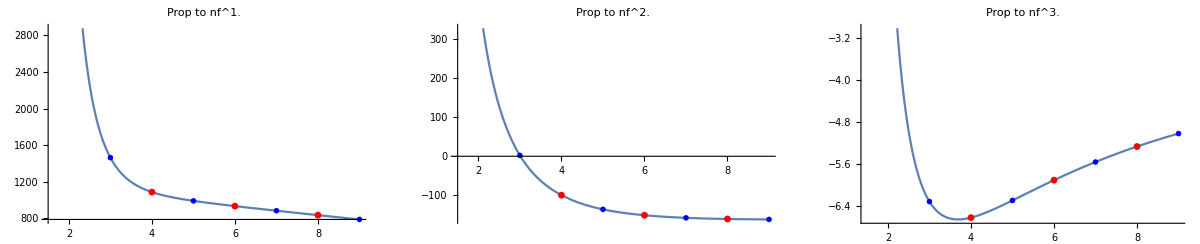

```mathematica
gqg3asytmp = gqg3N0asy+ gqg3N1asy + gqg3Ninf;
GraphicsRow[
	{PlotInterpolation[gqgmoments -gqg3asytmp, {1.1,3,5,7,9}, 1], PlotInterpolation[gqgmoments - gqg3asytmp, {1.5, 3,5,7,9}, 2], PlotInterpolation[gqgmoments -gqg3asytmp, {1.5,3,5,7,9}, 3]}
	, ImageSize->Full, PlotRange->All]
```

```mathematica
ref = gqg3nf3 - Coefficient[gqg3asytmp, nf, 3];
interpolator = MomentListInterpolator[gqgmoments-gqg3asytmp,{2,4,6,8},3] //Simplify ;
Table[
	Print["N: ",n, " Relative err (%): ",(ref - interpolator)/ ref * 100 //. QCDConstantsRules /. ZetaRules //N ], {n, 2,10}
];
```

N: 2 Relative err (%): -1.24594×10^-11

N: 3 Relative err (%): 2.36598

N: 4 Relative err (%): 3.08238×10^-13

N: 5 Relative err (%): 0.638497

N: 6 Relative err (%): 3.45496×10^-13

N: 7 Relative err (%): 0.394143

N: 8 Relative err (%): 3.53876×10^-13

N: 9 Relative err (%): 0.0390051

N: 10 Relative err (%): -0.453166

#### Fixing N = 3

```mathematica
flargeN = {{S13m1[n],S12m1[n]},{S13m1[n], S12m1[n]}, {S13m1[n],S12m1[n]}};

fSubLeadingLargeN = { 
	{Lm13[n],Lm13[n], Lm13[n]},
	{1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm11[n],Lm11[n], Lm11[n]}, 
	{Lm12[n],Lm12[n], Lm12[n]}, 
	{Lm13[n],Lm13[n], Lm13[n]}
};
fSubLeading = Join[fSubLeadingSmallN, fSubLeadingLargeN];

gqg3FittedInterpol = InterploatedFit[fsmallN, flargeN, fSubLeading, gqgmoments, gqg3N0asy, gqg3N1asy, gqg3Ninf, {3}];
```

```mathematica
gqg3invinterpol = ListMellinInverse[gqg3FittedInterpol];
gqg3invinterpol = SelectSmoothCandidates[gqg3invinterpol, 4,thrlow,thrlow];
```

Smooth candidates: 63 out of 66

```mathematica
GraphicsRow[ShowPlots[gqg3inv, gqg3invinterpol, gqg3asy, 4, {"cross candidates", "N=3"}], ImageSize -> Full]
```

-Graphics-

```mathematica
{graphQGint, graphQGlogint} =  PlotErrorBand[gqg3asy, gqg3invinterpol, 4, 2];
legend = {"cross candidate", "cherries", "N=3"}; 
GraphicsRow[{
      	ShowLegends[{graphQGlog, graphQGcherrylog, graphQGlogint}, LogLinearPlot, legend, {3,4,2}], 
      	ShowLegends[{graphQG, graphQGcherry, graphQGint}, Plot, legend, {3,4,2}]
      	}, ImageSize -> Full
  ]
```

-Graphics-

#### Save and final remove

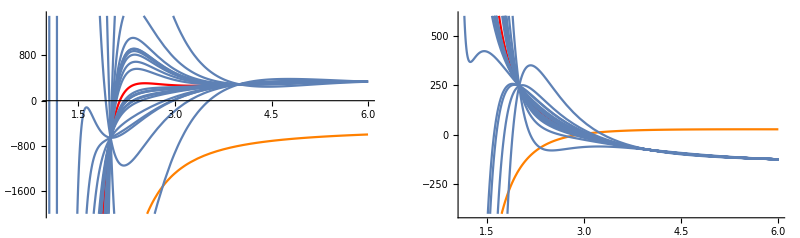

```mathematica
smoothcherryn = gqg3FittedCross[[Position[gqg3invfull, #]& /@ gqg3cherry //Flatten]] /. largeNrules // Simplify;
gqg3Nasy = gqg3N0asy + gqg3N1asy + gqg3Ninf;
g1 = PlotListN[gqg3Nasy, smoothcherryn, 1, -2000, 1500];
g2 = PlotListN[gqg3Nasy, smoothcherryn, 2, -400, 600];
GraphicsRow[{Show[g1, PlotRange-> All],Show[g2, PlotRange-> All]}, ImageSize->Full]
```

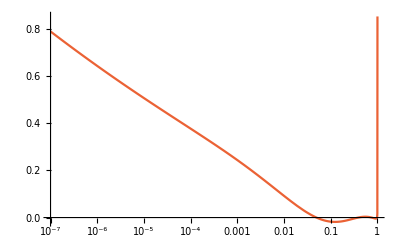
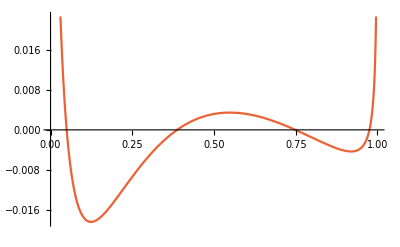
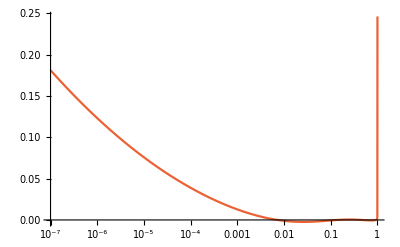
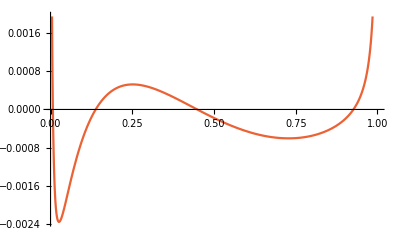
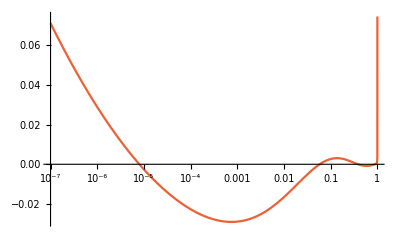
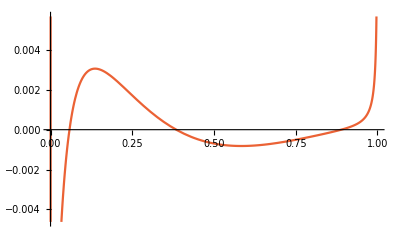
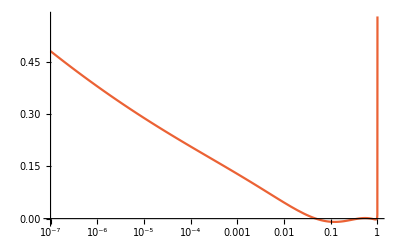
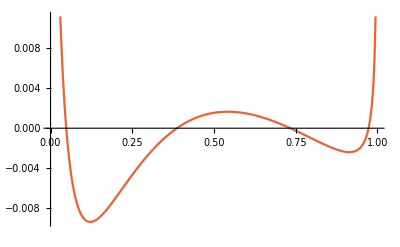
{{1,-Graphics-,-Graphics-},{2,-Graphics-,-Graphics-},{3,-Graphics-,-Graphics-},{4,-Graphics-,-Graphics-},{5,-Graphics-,-Graphics-},{6,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{9,-Graphics-,-Graphics-},{10,-Graphics-,-Graphics-},{11,-Graphics-,-Graphics-},{12,-Graphics-,-Graphics-},{13,-Graphics-,-Graphics-},{14,-Graphics-,-Graphics-},{15,-Graphics-,-Graphics-},{16,-Graphics-,-Graphics-},{17,-Graphics-,-Graphics-},{18,-Graphics-,-Graphics-},{19,-Graphics-,-Graphics-},{20,-Graphics-,-Graphics-},{21,-Graphics-,-Graphics-},{22,-Graphics-,-Graphics-}}

```mathematica
MapThread[{#1,#2, #3}& ,{ Range[1,graphQGcherryrep//Length ],graphQGcherrylogrep, graphQGcherryrep}]
```

To check: 1 and 7

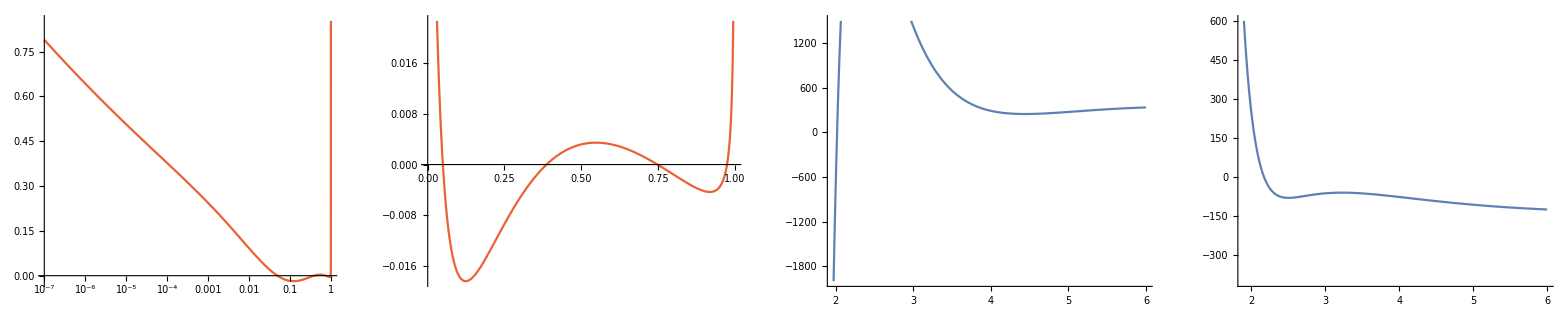

nf (-(2063.94 n nf)/(-1.+n)^2-(37.8062 nf^2)/n+(2.16816×10^6-111449. nf+106.118 nf^2)/n^4+(-205393.+11536.9 nf-14.2873 nf^2+n (38295.3+14.2873 nf^2))/(-1.+n)^2+(-699.679-12.8925 nf-1.04079 nf^2) S13m1[n])

```mathematica
posix = 1;
GraphicsRow[{LogPlotList[gqg3cherry, gqg3asy, 4, 4][[posix]], PlotList[gqg3cherry, gqg3asy, 4, 4][[posix]], g1[[posix+1]], g2[[posix+1]]}, ImageSize->Full]
smoothcherryn[[posix]]
```

Remove candidate 1

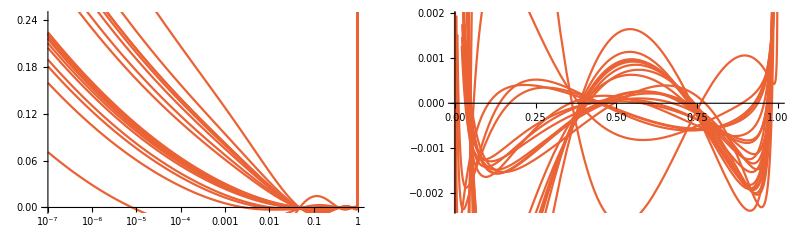

```mathematica
gqg3cherryrefined = Delete[gqg3cherry, 1];
graphQGcherrylogrepref = LogPlotList[gqg3cherryrefined, gqg3asy, 4, 4];
graphQGcherryrepref = PlotList[gqg3cherryrefined, gqg3asy, 4, 4];
GraphicsRow[{Show[graphQGcherrylogrepref], Show[graphQGcherryrepref]}]
```

```mathematica
{graphQGcherry1, graphQGcherrylog1} = PlotErrorBand[gqg3asy, gqg3cherryrefined, 4, 4]; 
legend = {"cross candidate", "cherries"};
GraphicsRow[{
    	ShowLegends[{graphQGlog, graphQGcherrylog1}, LogLinearPlot, legend, {3, 4}], 
    	ShowLegends[{graphQG, graphQGcherry1}, Plot, legend, {3, 4}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

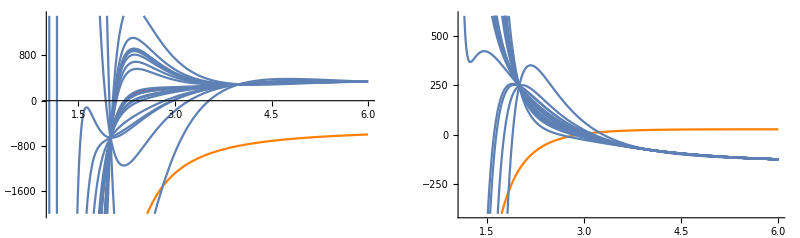

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqg3nf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/gqg3nf2.c

```mathematica
smoothcherryn = gqg3FittedCross[[Position[gqg3invfull, #]& /@ gqg3cherry //Flatten]] /. largeNrules // Simplify;
smoothcherryn = Delete[smoothcherryn, 1];
gqg3Nasy = gqg3N0asy + gqg3N1asy + gqg3Ninf;
g1ref = PlotListN[gqg3Nasy, smoothcherryn, 1, -2000, 1500];
g2ref = PlotListN[gqg3Nasy, smoothcherryn, 2, -400, 600];
GraphicsRow[{Show[g1ref, PlotRange-> All],Show[g2ref, PlotRange-> All]}, ImageSize->Full]


exportMeList[gqg3Nasy, smoothcherryn, StringJoin[storepath, "gqg3nf1.c"], 1];
exportMeList[gqg3Nasy, smoothcherryn, StringJoin[storepath, "gqg3nf2.c"], 2];
```

```mathematica
smoothcherryn//Length
```

21